```mathematica
n=11;
```

```mathematica
(*k=AdjacencyMatrix[RandomGraph[{n,21}]];
AdjacencyGraph[k]*)
```

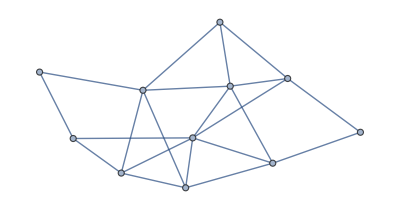
```mathematica
k1=-Graphics-;
```

```mathematica
k=AdjacencyMatrix[k1]
```

SparseArray[<42>, {11, 11}]

```mathematica
data={0.6562722556236429,-0.34657670139825003,0.23728565072404703,-0.5347469428961505,1.8997829817652392,1.4296796397474802,-1.735727298690614,-1.7816500083767144,2.277924371534762,1.3312030304500866,-0.06828965655804965};
```

```mathematica
m=3;
(*data=RandomVariate[VonMisesDistribution[0,0],n];*)
cmsol=Solve[1+a Sum[(m+1-mm)Cos[(2mm Pi)/(m+1)],{mm,1,m}]==0,a];
cmkoef=a/.cmsol[[1]];
eqns=Table[{Subscript[∅,i]'[t]==-1/n Sum[k[[i]][[j]](cmkoef Sum[mm(m+1-mm)Sin[mm(Subscript[∅,j][t]-Subscript[∅,i][t])],{mm,1,m}]),{j,1,n}],Subscript[∅,i][0]==data[[i]]},{i,1,n}];
vars=Table[Subscript[∅,i][t],{i,1,n}];
sol=NDSolve[eqns,vars,{t,0,10000}];
Do[Subscript[z,i][t_]:=Evaluate[Subscript[∅,i][t]/.sol],{i,1,n}];
Do[Subscript[zz,i][t_]:=Evaluate[ⅇ^(ⅈ×Subscript[∅,i][t]/.sol)],{i,1,n}];
data1[t_]:=Flatten[Table[Subscript[zz,i][t],{i,1,n}]];
tt=10000;
lista=Sort[Table[Mod[Subscript[z,i][tt],2Pi][[1]],{i,1,n}]];
lisboj[t_]:=Table[Mod[Subscript[z,i][t],2Pi][[1]],{i,1,n}];
SomeGraph=AdjacencyGraph[k];
Table[lista[[i]]-lista[[i+1]],{i,1,n-1}]
ukupfrust[t_]:=Sum[k[[i]][[j]](1+cmkoef Sum[(m+1-mm)Cos[mm(Subscript[z,j][t]-Subscript[z,i][t])],{mm,1,m}]),{i,1,n},{j,i+1,n}]
ukupfrust[5000]
```

{-1.11022×10^-16,-1.5708,0.,0.,-1.5708,0.,0.,-4.44089×10^-16,-1.5708,0.}

{7.77156×10^-16}

```mathematica
granica=22;
```

```mathematica
video[t_]:=Grid[{{GraphPlot[SomeGraph,PlotStyle->{Gray,Thickness[0.008]},VertexRenderingFunction->Function[{pos,vid},{(*color for the disk*)Hue@Rescale[lisboj[t][[Sequence@@vid]],{0,2 Pi}],(*the disk itself*)Disk[pos,0.17],(*vertex number centered on the disk*)Text[Style[vid,20,Black,Bold],pos]}],ImageSize->700],Show[Module[{pts},pts=ReIm@data1[t];
ListPlot[pts,PlotStyle->{Black,Opacity[0],PointSize[0.025]},Epilog->MapIndexed[Text[Style[#2[[1]],16,Black,Bold],#1+{0.045,0.045}   (*small offset*)]&,pts]]],With[{sectors=360},angle=2 Pi/sectors;
Graphics[{Table[{Hue[i/sectors],EdgeForm[{Thick,Hue[i/sectors]}],Disk[{0,0},1,{i angle,(i+1) angle}]},{i,0,sectors-1}]}]],Module[{pts},pts=ReIm@data1[t];
ListPlot[pts,PlotStyle->{Black,PointSize[0.025]},Epilog->MapIndexed[Text[Style[#2[[1]],14,Black,Bold],#1+{0.03,0.03}   (*small offset*)]&,pts]]],ImageSize->Large,Frame->True,FrameStyle->Directive[Black,25],Axes->True,AxesOrigin->{0,0},PlotRange->{{-1.1,1.1},{-1.1,1.1}},ImagePadding->40,AspectRatio->1],Show[{Plot[ukupfrust[tt],{tt,0,t+0.0000000001},PlotRange->{{0,granica},{0,ukupfrust[0][[1]]}},PlotStyle->Directive[If[Chop[ukupfrust[10000]][[1]]==0,Red,Blue],Thickness[0.01]]]},AxesOrigin->{0,0},PlotRange->{{0,granica},{0,ukupfrust[0][[1]]}},ImageSize->600,Frame->True,FrameStyle->Directive[Black,25]]}},Spacings->0]
```

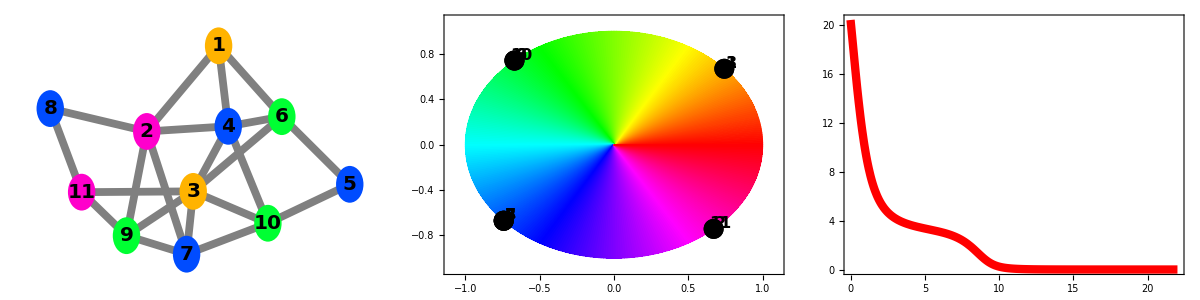

```mathematica
video[22]
```

```mathematica
simulaci1=Table[video[t],{t,0,22,0.02}];
```

```mathematica
Export["SM1.AVI",simulaci1]
```

video_boj_bez_zvuka_unif.AVI